```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
<<GDCComparisons`
<<GDCAnalysis3`
```

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

```mathematica
filesAR=FileNames["/home/carla/GDC/CH_Pool/PHI/GDC_CHP_AR_PHI_ALL_Out/*.txt"];
inputAR=Map[Get[#]&, filesAR];
dojAR=inputAR[[All,1]];
zAR=inputAR[[All,2]];
fAR=inputAR[[All,3]];
filesBR=FileNames["/home/carla/GDC/CH_Pool/PHI/GDC_CHP_BR_PHI_ALL_Out/*.txt"];
inputBR=Map[Get[#]&, filesBR];
dojBR=inputBR[[All,1]];
zBR=inputBR[[All,2]];
fBR=inputBR[[All,3]];
```

```mathematica
(*MIN Values*)
Map[dojBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[zBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[fBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
```

{0.000198255,0.,0.,0.,0.,0.}

{-0.112698,-1.,-1.,-1.,-1.,-1.}

{-0.0598016,-1,-1,-1,-1,-1}

```mathematica
tsAR={2,3,4,5,6,7,8};
tsBR={2.5,3.5,4.5,5.5,6.5,7.5};
tsAll=Union[tsAR,tsBR];
```

```mathematica
dojMax=maxValFunc[tsAR, tsBR, dojAR, dojBR, "PHI", "DOJ"]
zMax=maxValFunc[tsAR, tsBR, zAR, zBR, "PHI", "Z"]
fMax=maxValFunc[tsAR, tsBR, fAR, fBR, "PHI", "F"]
```

{{2,0.00138779},{2.5,0.00138779},{3,0.010101},{3.5,0.010101},{4,0.0333333},{4.5,0.0439691},{5,0.0222222},{5.5,0.0133333},{6,0.0133333},{6.5,0.0133333},{7,0.04},{7.5,0.0416667},{8,1.}}

{{2,0.00077295},{2.5,0.000791212},{3,0.00970624},{3.5,0.00968605},{4,0.0325298},{4.5,0.0424875},{5,0.0216303},{5.5,0.0129991},{6,0.0129991},{6.5,0.0130032},{7,0.0396788},{7.5,0.0413485},{8,1.}}

{{2,0.481255},{2.5,0.49829},{3,0.924776},{3.5,0.92108},{4,0.952926},{4.5,0.950229},{5,0.948106},{5.5,0.951095},{6,0.951095},{6.5,0.951673},{7,0.984066},{7.5,0.984844},{8,1}}

```mathematica
dojTat=Get["/home/carla/GDC/CONF/PHI/PHI_DOJ.txt"]
zTat=Get["/home/carla/GDC/CONF/PHI/PHI_Z.txt"]
fTat=Get["/home/carla/GDC/CONF/PHI/PHI_F.txt"]
```

{{2,0.000793021},{2.5,0.000793021},{3,0.00505051},{3.5,0.00505051},{4,0.0333333},{4.5,0.0231729},{5,0.0222222},{5.5,0.0133333},{6,0.0133333},{6.5,0.0133333},{7,0.04},{7.5,0.0416667},{8,1.}}

{{2,0.000515229},{2.5,0.000527404},{3,0.00478602},{3.5,0.00477249},{4,0.0322929},{4.5,0.0225747},{5,0.0216234},{5.5,0.0129954},{6,0.0129954},{6.5,0.0129994},{7,0.0396751},{7.5,0.0413448},{8,1.}}

{{2,0.481156},{2.5,0.498191},{3,0.900476},{3.5,0.895651},{4,0.939461},{4.5,0.949666},{5,0.94752},{5.5,0.950567},{6,0.950567},{6.5,0.95114},{7,0.983888},{7.5,0.984669},{8,1}}

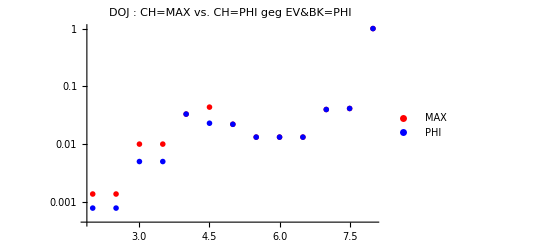
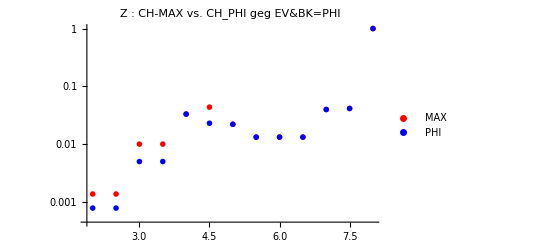
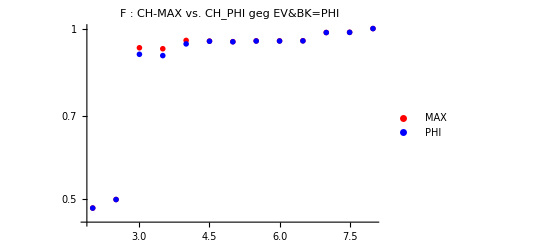

```mathematica
dojPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "PHI"},PlotStyle->{Red, Blue},PlotLabel->"DOJ : CH=MAX vs. CH=PHI geg EV&BK=PHI",PlotMarkers->{{"X",12}, {"P",12}},ImageSize->400];
zPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "PHI"},PlotStyle->{Red, Blue},PlotLabel->"Z : CH-MAX vs. CH_PHI geg EV&BK=PHI",PlotMarkers->{{"X",12}, {"P",12}},ImageSize->400];
fPlot=ListLogPlot[{fMax,fTat},PlotLegends->{"MAX", "PHI"},PlotStyle->{Red, Blue},PlotLabel->"F : CH-MAX vs. CH_PHI geg EV&BK=PHI",PlotMarkers->{{"X",12}, {"P",12}},ImageSize->400];
confMAX=Column[{dojPlot,zPlot,fPlot}]
```

```mathematica
(* dojBR[[5,2]][["value"]]
dojTat[[10]]
dojBR[[5,2]][["list"]][[1;;3]]
Map[compCHMaxFunc[First[persMixFunc["PHI"]], #, tatCH , dojBR]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["PHI"]],# , tatCH, "CH", "PEN"]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["PHI"]],# , dojBR,  "CH", "PEN"]&,{4.5}]*)
```

```mathematica
tatCH=Map[Get[#]&,FileNames["/home/carla/GDC/POS/*.txt"]];
persInd=First[persMixFunc["PHI"]]
```

11

```mathematica
(*VV-Value von CH-TAT : Ähnlichkeit von CH-TAT mit DEV*)
Map[{#,vvPosFunc[persInd,# , tatCH, "CH", "PEN"]}&,tsAR]
```

{{2,0.6},{3,0.6},{4,0.8},{5,0.8},{6,0.8},{7,0.8},{8,1.}}

```mathematica
(*Veritistic Value von CH-MAX : Ähnlichkeit von CH_MAX mit DEV*)
dojVV=vvCHMaxFunc[tsAR, tsBR, dojAR, dojBR,persInd];
zVV=vvCHMaxFunc[tsAR, tsBR, zAR, zBR,persInd];
fVV=vvCHMaxFunc[tsAR, tsBR, fAR, fBR,persInd];
dojVVHist=vvHistPointsFunc[dojVV];
zVVHist=vvHistPointsFunc[zVV];
fVVHist=vvHistPointsFunc[fVV];
```

13

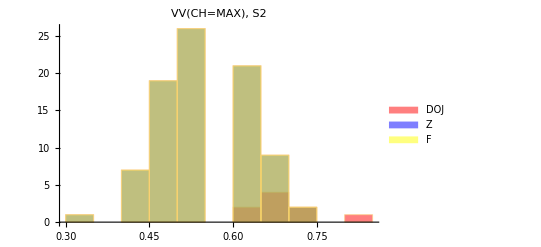
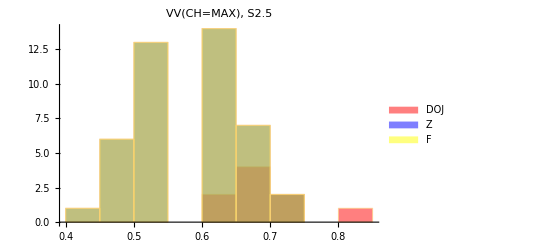
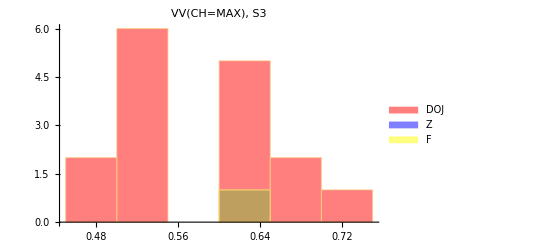
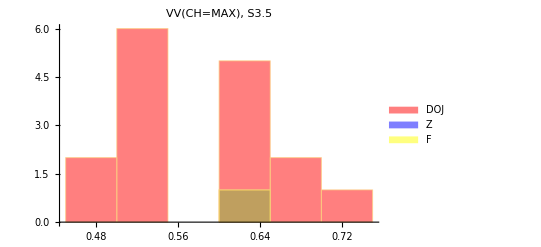
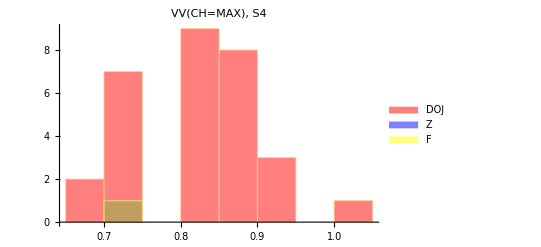
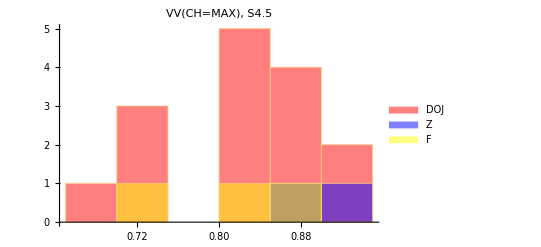
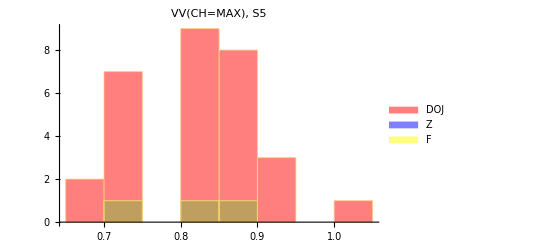
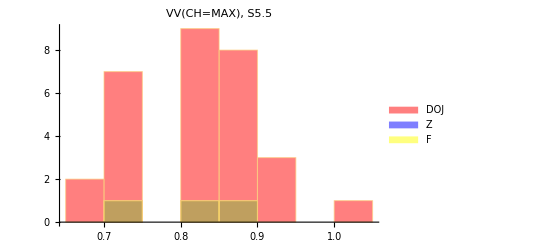
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | GrayLevel[1] | GrayLevel[1]

```mathematica
(*ListPlot[dojVVHist,PlotLegends->{"DOJ"},PlotStyle->{Red},PlotLabel->"VV CH=MAX geg EV&BK=PHI",PlotMarkers->{{"D",12}}, PlotRange->All]
ListPlot[zVVHist, PlotLegends->{"Z"},PlotStyle->{Blue},PlotLabel->"VV CH=MAX geg EV&BK=PHI",PlotMarkers->{{"Z",12}}, PlotRange->All]
ListPlot[fVVHist, PlotLegends->{"F"},PlotStyle->{Green},PlotLabel->"VV CH=MAX geg EV&BK=PHI",PlotMarkers->{{"F",12}}, PlotRange->All]
vvMaxPlot=ListPlot[{dojVVHist,zVVHist,fVVHist}, PlotLegends->{"DOJ","Z","F"},PlotStyle->{Red,Blue,Green},PlotLabel->"VV CH=MAX geg EV&BK=PHI",PlotMarkers->{{"D",12},{"Z",12},{"F",12}}, PlotRange->{0,1.05}]*)
timL={2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8};
Length[timL]
hist=Map[Histogram[{dojVV[[#,2]],zVV[[#,2]],fVV[[#,2]]}, PlotLabel->"VV(CH=MAX),    S"<>ToString[timL[[#]]],ImageSize->400, ChartLegends->{"DOJ","Z","F"},ChartStyle->{Red,Blue,Yellow}]&,Range[Length[timL]]];
histOut=Grid[{hist[[1;;3]],hist[[4;;6]],hist[[7;;9]],hist[[10;;12]],{hist[[13]],White,White}},ItemSize->35]
```

```mathematica
SetDirectory["/home/carla/GDC/CH_Pool/PHI/"];
Export["COMP_DOJ_CHTAT_CHMAX_PHI.jpeg",dojPlot,ImageResolution->300]
Export["COMP_CHTAT_CHMAX_PHI.jpeg",confMAX,ImageResolution->300]
Export["VV_CHMAX_HIST_PHI.jpeg",histOut,ImageResolution->300]
Put[dojVVHist, "gdc_DOJ_VV_CHMAX_PHI.txt"]
Put[zVVHist, "gdc_Z_VV_CHMAX_PHI.txt"]
Put[fVVHist, "gdc_F_VV_CHMAX_PHI.txt"]
```

COMP_DOJ_CHTAT_CHMAX_PHI.jpeg

COMP_CHTAT_CHMAX_PHI.jpeg

VV_CHMAX_HIST_PHI.jpeg